```mathematica
Clear["Global`*"]
folder ="C:\\Users\\jerzy\\Downloads\\";
folder2= "C:\\Users\\jerzy\\Licencjat\\";
Import[folder<>"qfold.mx"]
Import[folder<>"qneck.mx"]
Import[folder<>"linerfold.mx"]
$Assumptions = p>0&&r>0&&n0>1&&n1>1&&Q>0&&u>0;
qfletcher[p_, r_, n0_, n1_] = Simplify[q[p, r, n0, Q]/.Q->Sqrt[n0/n1]*r];
neck[λ_,r_,n0_,n1_,u_]=Simplify[-1 + qneck[2π/λ, r, n0, n1, u]];
fold[λ_, r_, n0_, n1_,u_] = Simplify[1 - qfold[2π/λ, r, n0, n1, u]];
liner[λ_, r_, u_] = Simplify[1-linerfold[2π/λ, r, u]];
fletcher[λ_, r_, n0_, n1_] = Simplify[1- qfletcher[2π/λ, r, n0, n1]];
```

```mathematica
Clear[plots];
plots = {}; j=1;
Manipulate[plt = LogLinearPlot[fold[λ,r,n0,n1,u], {λ, 0.5, 1000},PlotStyle->{Thick,ColorData[63,"ColorList"][[j]]}, ImageSize->500,Frame->{True,True,False,False},FrameLabel->{Style["λ/H",Orange,FontSize->13],Style["1-q",Purple,FontSize->14]},(*PlotLabel->Style["Skończony n_0="<>ToString[Round[n0]]<>" n_1="<>ToString[Round[n1]]<>" u="<>ToString[u],FontSize->15], *)AspectRatio->1, PlotRange->All, RotateLabel->False, PlotLabels->Placed[Style["n_0="<>ToString[Round[n0]]<>" n_1="<>ToString[Round[n1]]<>"\n r="<>ToString[r]<>" u="<>ToString[u],FontSize->10], Above]],
Button["Export",Export[folder<>"\\Finite\\"<>ToString[Round[n0]]<>"."<>ToString[Round[n1]]<>"."<>ToString[u]<>".png",plt]],{plt,ControlType->None},
{n0, 1.001, 10.01, 1, Appearance->"Labeled"}, {n1, 1.001, 10.01, 1, Appearance->"Labeled"}, {{r, 0.01}, -3, -1, Row@{Manipulator[Dynamic[Log[10, #1],(r=10^#1)&],  #2]," ",InputField[Dynamic@r]}&},
{{u, 100}, 10, 0, Row@{Manipulator[Dynamic[Log[2, #1],(u=2^#1)&],  #2]," ",InputField[Dynamic@u]}&},
Button["Add Plot", AppendTo[plots, {r, n0, n1, u}]; j+=1;]]
```

{{0.005,2,5,26},{0.01,5,5,15},{0.01,7,7,16},{0.02,3,5,14.5}}

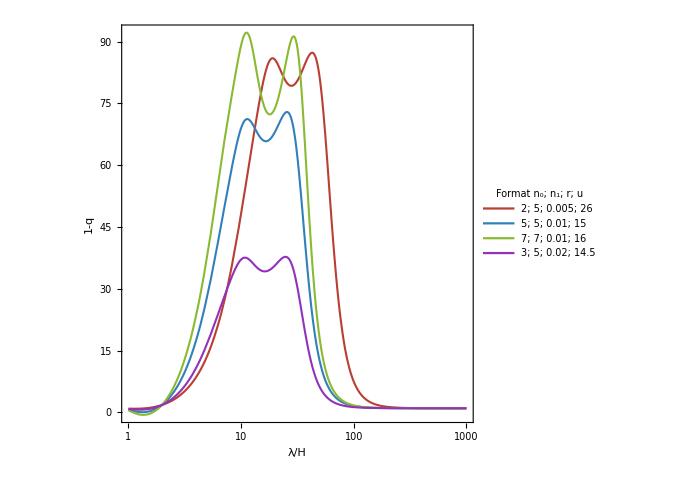

```mathematica
plots = {{0.005, 2, 5, 26}, {0.01, 5,5, 15}, {0.01, 7, 7, 16}, {0.02, 3, 5, 14.5}}
plt = LogLinearPlot[Evaluate[fold[λ,#1,#2,#3, #4] & [Sequence@@#]&/@plots], {λ, 1, 1000},PlotStyle->(Directive[ColorData[63,"ColorList"][[#]], Thickness[0.003]]&/@Range[Length[plots]]),ImageSize->500,Frame->{True,True,False,False},FrameLabel->{Style["λ/H",Orange,FontSize->13],Style["1-q",Purple,FontSize->14]},AspectRatio->1, PlotRange->All, RotateLabel->False,
PlotLegends->LineLegend[ColorData[63,"ColorList"][[;;Length[plots]]],ToString[Round[#2]]<>"; "<>ToString[Round[#3]]<>"; "<>ToString[#1]<>"; "<>ToString[#4]&[Sequence@@#]&/@plots, LegendLabel->"Format n_0; n_1; r; u"]]
```

```mathematica
Export[folder2<>"double.png",plt, ImageResolution->500]
```

C:\Users\jerzy\Licencjat\double.png

```mathematica
Directive[ColorData[63,"ColorList"][[#]],Thick]&/@Range[Length[plots]]
```

{Directive[RGBColor[0.73, 0.24506099999999992, 0.1971],Thickness[Large]],Directive[RGBColor[0.1971, 0.5022473119339774, 0.73],Thickness[Large]],Directive[RGBColor[0.5356156238679548, 0.73, 0.1971],Thickness[Large]],Directive[RGBColor[0.5712760641980676, 0.1971, 0.73],Thickness[Large]],Directive[RGBColor[0.1971, 0.73, 0.5379077522640902],Thickness[Large]],Directive[RGBColor[0.73, 0.5045394403301129, 0.1971],Thickness[Large]],Directive[RGBColor[0.1971, 0.24276887160386468, 0.73],Thickness[Large]]}

```mathematica
testowe[p_,u_]=Simplify[Limit[linerfold[p, r, u], r->0, Direction->"FromAbove"]]
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

(2 p)/(p-Sinh[p])

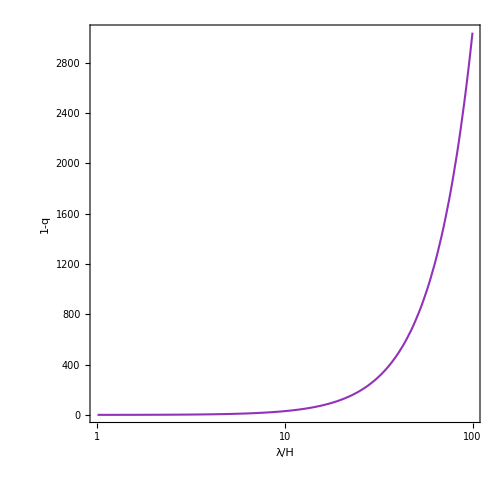

```mathematica
LogLinearPlot[1-testowe[2π/λ,15], {λ, 1, 100},PlotStyle->(Directive[ColorData[63,"ColorList"][[#]], Thickness[0.003]]&/@Range[Length[plots]]),ImageSize->500,Frame->{True,True,False,False},FrameLabel->{Style["λ/H",Orange,FontSize->13],Style["1-q",Purple,FontSize->14]},AspectRatio->1, PlotRange->All, RotateLabel->False]
```